# Retrospective evaluation of school-related measures on pre-vaccination transmission dynamics of SARS-CoV-2

## Benedetta Canfora, Rey Audie Escosio, Christiaan H. van Dorp, Otilia Boldea, Marc Bonten, Ana Nunes, and Ganna Rozhnova* Corresponding author: g.rozhnova@umcutrecht.nl

## Sensitivity analysis on school mitigation levels

## Global parameters

```mathematica
(* Clear *)
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Off[General::munfl]
SetDirectory[NotebookDirectory[]];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

### Packages and parameters

```mathematica
(* External packages *)
AppendTo[$Path,"../packages"];
Needs["plotting`"];
Needs["preliminaries`"];

createResultDirectories[];

(*Remove["plotting`*"]
Get["../packages/plotting.m"]*)

(* Notebook parameters *)
ifShowFigs= True;
ifExportData = False;
ifExportFigs = False;
exportFormat={".pdf",".eps"};

(* Known constants *)
(* Age groups *)
numAgeGroups = 10;
listAgeGroups= Table[k, {k, 1, numAgeGroups}];
listChildren = Range[1,3];
listAdults = Range[4,10];
groupIndex = {listChildren, listAdults};

(* Samples *)
numAllSamples = 2000;
stepSamples=20; (* 20 corresponds to 100 samples *)
listSamples=Table[i,{i,1,numAllSamples,stepSamples}];
numSamples = Length[listSamples];

(* Variables *)
numVariables=5;
varNumbers= Table[j, {j, 1, numVariables}];
eqNumbers=Table[k,{k,1,numAgeGroups numVariables}];

(* Scenarios *)
scenarios={"Baseline","Scenario1_10","Scenario1_20","Scenario1_30","Scenario1_40","Scenario1_50","Scenario1_60","Scenario1_70","Scenario1_80","Scenario1_90", "Scenario1","Scenario2_10","Scenario2_20","Scenario2_30","Scenario2_40","Scenario2_50","Scenario2_60","Scenario2_70","Scenario2_80","Scenario2_90", "Scenario2"};
numScenarios = Length[scenarios];
```

```mathematica
scen1Idx = Range[1,11];
scen2Idx = {1,12,13,14,15,16,17,18,19,20,21};
```

### Important dates and time step

```mathematica
(* Date of starting simulations: February 25, 2020 *)
timeStart=0;
(* Date of start of the pandemic: February 26, 2020 *)

(* Date of last hospitalization/last data point: January 15, 2021 *)
timeEndData = Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 ; (* Jan 15 but starting with t=1 *)


(* Integration end-time and time step *)
tStep=1;
tEnd=timeEndData;
tStart=timeStart;
times =Range[tStart,tEnd,tStep];
numTimes = Length[times];

(* Scenario time points *)
tStart1="February 25, 2020";
tEnd1="July 15, 2020";
tStart2="July 15, 2020";
tEnd2="January 16, 2021";
```

## Demography and contact matrices

### Seroprevalence data

```mathematica
totalMeanSero=2.9;
totalLowMeanSero=2.0;
totalHighMeanSero=4.2;
seroTotalDataAround = Around[totalMeanSero, {Abs[totalMeanSero - totalLowMeanSero], Abs[totalHighMeanSero-totalMeanSero]}];

seroprevalenceData=100 * Drop[Import["../data/PT_SEROPREVALENCE_DATA.csv"],1][[All,5;;7]];
seroAgeDataAround=Table[Around[seroprevalenceData[[i,1]],{seroprevalenceData[[i,1]] - seroprevalenceData[[i,2]],seroprevalenceData[[i,3]] - seroprevalenceData[[i,1]]}],{i,1,Length[seroprevalenceData]}];

seroDataMay28Around =Flatten[ {seroTotalDataAround, seroAgeDataAround}];
```

### Contact matrices from Vespignani et al.

```mathematica
(* Importing Data *)
(* https://github.com/mobs-lab/mixing-patterns *)
demographyData85=Import["../data/PT_DEMOGRAPHY_DATA_85.csv"]⟦All,2⟧;
contactDataBefore85=Import["../data/PT_CONTACT_MATRIX_TOTAL_85.csv"];
schoolContactDataBefore85=  11.41 * Import["../data/PT_CONTACT_MATRIX_SCHOOL_85.csv"];


(* Get the total contacts per participant *)
calculateTotalContsPerPar[conmat_, groupNo_] := Table[Total[conmat⟦k,All⟧],{k,groupNo}];
```

### Transforming the contact matrices from 86x86 to 10x10

```mathematica
(* Demographic data for 86+
https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
demog86Plus = 316442;

(* Getting the ratio of lockdown contacts based on NL data *)
contactDataNLBefore10=Import["../data/NL_CONTACT_MATRIX_BEFORE_10.csv"];
contactDataNLAfter10=Import["../data/NL_CONTACT_MATRIX_AFTER_10.csv"];
contactRatioNL10=contactDataNLAfter10/contactDataNLBefore10;
demographyData10=Flatten[Import["../data/PT_DEMOGRAPHY_DATA_10.xlsx"]];

(* Function transforming the 1x86 age groups to 1x10 *)
transformList86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
demographyData86=Append[demographyData85, demog86Plus];
demographyData10Derived=transformList86to10[demographyData86];


(* Creating the 86x86 contact matrices *)
transformMatrix85to86[mat85_]:=Join[Join[mat85,{mat85⟦85⟧}],List/@(Join[mat85,{mat85⟦85⟧}]⟦All,85⟧ demographyData86⟦86⟧/demographyData86⟦85⟧), 2];
contactDataBefore86=transformMatrix85to86[contactDataBefore85];
schoolContactDataBefore86=transformMatrix85to86[schoolContactDataBefore85];


(* Creating the 10x10 contact matrices*)
transformMatrix86to10[mat86_] :=transformList86to10[Transpose[transformList86to10[Transpose[mat86]]] demographyData86]/demographyData10Derived;
fileContactBefore10="../data/RES_PT_CONTACT_MATRIX_BEFORE_10.csv";
fileContactAfter10="../data/RES_PT_CONTACT_MATRIX_AFTER_10.csv";
fileSchoolBefore10="../data/RES_PT_CONTACT_MATRIX_SCHOOL_10.csv";
If[FileExistsQ[fileContactBefore10]&&FileExistsQ[fileContactAfter10]&&FileExistsQ[fileSchoolBefore10],

contactDataBefore10=Import[fileContactBefore10, "Table","FieldSeparators"->"\t"];
contactDataAfter10=Import[fileContactAfter10, "Table","FieldSeparators"->"\t"];
schoolContactDataBefore10=Import[fileSchoolBefore10, "Table","FieldSeparators"->"\t"];
,

contactDataBefore10=transformMatrix86to10[contactDataBefore86];
contactDataAfter10=contactDataBefore10 * contactRatioNL10 ;
schoolContactDataBefore10=transformMatrix86to10[schoolContactDataBefore86];

Export[fileContactBefore10,contactDataBefore10, ];
Export[fileContactAfter10,contactDataAfter10];
Export[fileSchoolBefore10,schoolContactDataBefore10];
]

(* Get the total contacts per participant *)
calculateContactsAgeGroupsBefore=calculateTotalContsPerPar[contactDataBefore10, numAgeGroups];
calculateSchoolContactsAgeGroupsBefore=calculateTotalContsPerPar[schoolContactDataBefore10, numAgeGroups];
calculateContactsAgeGroupsAfter=calculateTotalContsPerPar[contactDataAfter10, numAgeGroups];

(* Get the average contacts per participant *)
calculateAverageContactRateBefore=Sum[calculateContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateSchoolsBefore=Sum[calculateSchoolContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateAfter=Sum[calculateContactsAgeGroupsAfter⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
```

## Hospitalization data and estimated parameters

### Estimated parameters

```mathematica
(* Importing estimated parameters *)
estimatesData=Import["../data/PARAMETER_ESTIMATES.csv"];
headerParameters=estimatesData⟦1⟧;
estimatesData=Drop[estimatesData,1];
```

```mathematica
(* Total population *)
totalPop=Table[Subscript[NN,k]->demographyData10[[k]],{k,listAgeGroups}];

(* Contact matrix variables *)
contactRates=Flatten[Table[{Subscript[b,{k,l}]->contactDataBefore10[[k,l]],Subscript[a,{k,l}]->contactDataAfter10[[k,l]],Subscript[s,{k,l}]->schoolContactDataBefore10[[k,l]]},{k,1,numAgeGroups},{l,1,numAgeGroups}]];

(* Table for all parameters; also assigning variables *)
parametersComplete[sample_Integer]:=
Module[{est},
est=estimatesData[[sample]];
Flatten[{contactRates,totalPop,
(* Age-independent parameters *)
ϵ->est[[1]],ζ->est[[2]],α->est[[18]],γ->est[[19]],
(* Hospitalization rate *)
Table[Subscript[ν,k]->est[[2+k]],{k,1,numAgeGroups}],(* Initial conditions *)Table[{Subscript[S0,k]->1-est[[13]],Subscript[EE0,k]->0.5*est[[13]],Subscript[II0,k]->0.5*est[[13]],Subscript[R0,k]->0,Subscript[H0,k]->0},{k,listAgeGroups}],
(* Susceptibility *)
Table[Subscript[β,k]->est[[14]],{k,1,3}],Table[Subscript[β,k]->est[[15]],{k,4,7}],Table[Subscript[β,k]->est[[16]],{k,8,10}],
(* Logistic function parameters *){Subscript[xx,0]->est[[20]],Subscript[K,0]->est[[21]],Subscript[xx,1]->est[[22]],Subscript[K,1]->est[[23]],Subscript[xx,2]->est[[24]],Subscript[K,2]->est[[25]],Subscript[xx,3]->est[[26]],Subscript[K,3]->est[[27]],Subscript[xx,4]->est[[28]],Subscript[K,4]->est[[29]]},
{Subscript[u,1]->est[[30]],Subscript[u,2]->est[[31]],Subscript[u,3]->est[[32]],Subscript[u,4]->est[[33]]}}]];

(* Sampled parameters *)
parametersCompleteSampled=Table[parametersComplete[i],{i,1,numAllSamples,stepSamples}];
```

### Hospitalization data

```mathematica
(* Importing data *)hospitalizationData=Import["../data/PT_HOSPITALIZATION_DATA.csv"];
hospitalizationData=Drop[hospitalizationData,1];
hospitalizationDataTotal =Total[hospitalizationData, {2}];
hospitalizationDataGrouped = {Total[hospitalizationData[[All, 4;;10]], {2}], Total[hospitalizationData[[All, 1;;3]], {2}]};


(* Transition dates and their respective quantiles *)transitionDates=Table[DayPlus[{2020,02,25}, IntegerPart[Median[estimatesData⟦All,index⟧]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles025=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.025]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles975=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.975]]],{index,Range[20,28,2]}]; 
(* Range[20,28,2] are the indices for transition dates *)
```

## Equations and variables

### Expressions for contact matrices

```mathematica
contactMatrixBaseline[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));


(* SCENARIO 1 *)
(* Schools remained open during LD1 before transitioning to the first relaxation of measures *)
contactMatrixScenario1[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));


(* SCENARIO 2 *)
(* Schools remained closed after the 2020 summer holidays spanning Relax 2, LD 2, and Relax 3 *)
contactMatrixScenario2[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-Subscript[u, 4] Subscript[s,{k,l}]); 




contactMatrixScenario110[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + 0.10*Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));
contactMatrixScenario120[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + 0.20*Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));
contactMatrixScenario130[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + 0.30*Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));
contactMatrixScenario140[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + 0.40*Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));
contactMatrixScenario150[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + 0.50*Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));
contactMatrixScenario160[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + 0.60*Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));
contactMatrixScenario170[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + 0.70*Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));
contactMatrixScenario180[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + 0.80*Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));
contactMatrixScenario190[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + 0.90*Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));



contactMatrixScenario210[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-0.10*Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-0.10*Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-0.10*Subscript[u, 4] Subscript[s,{k,l}]); 
contactMatrixScenario220[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-0.20*Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-0.20*Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-0.20*Subscript[u, 4] Subscript[s,{k,l}]); 
contactMatrixScenario230[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-0.30*Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-0.30*Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-0.30*Subscript[u, 4] Subscript[s,{k,l}]); 
contactMatrixScenario240[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-0.40*Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-0.40*Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-0.40*Subscript[u, 4] Subscript[s,{k,l}]); 
contactMatrixScenario250[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-0.50*Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-0.50*Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-0.50*Subscript[u, 4] Subscript[s,{k,l}]); 
contactMatrixScenario260[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-0.60*Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-0.60*Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-0.60*Subscript[u, 4] Subscript[s,{k,l}]); 
contactMatrixScenario270[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-0.70*Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-0.70*Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-0.70*Subscript[u, 4] Subscript[s,{k,l}]); 
contactMatrixScenario280[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-0.80*Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-0.80*Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-0.80*Subscript[u, 4] Subscript[s,{k,l}]); 
contactMatrixScenario290[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-0.90*Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-0.90*Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-0.90*Subscript[u, 4] Subscript[s,{k,l}]);
```

### Model equations

```mathematica
(* Table of equations *)Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t],eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t],
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t],
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]},{k,listAgeGroups}];
NNtot=Sum[Subscript[NN,k],{k,listAgeGroups}];
```

```mathematica
(* The contact matrix to use *)contactMatrix["Baseline",t_]:=contactMatrixBaseline[t];
contactMatrix["Scenario1",t_]:=contactMatrixScenario1[t];
contactMatrix["Scenario2",t_]:=contactMatrixScenario2[t];
contactMatrix["Scenario2_50",t_]:=contactMatrixScenario250[t];
contactMatrix["Scenario2_10",t_]:=contactMatrixScenario210[t];
contactMatrix["Scenario2_20",t_]:=contactMatrixScenario220[t];
contactMatrix["Scenario2_30",t_]:=contactMatrixScenario230[t];
contactMatrix["Scenario2_40",t_]:=contactMatrixScenario240[t];
contactMatrix["Scenario2_60",t_]:=contactMatrixScenario260[t];
contactMatrix["Scenario2_70",t_]:=contactMatrixScenario270[t];
contactMatrix["Scenario2_80",t_]:=contactMatrixScenario280[t];
contactMatrix["Scenario2_90",t_]:=contactMatrixScenario290[t];
contactMatrix["Scenario1_50",t_]:=contactMatrixScenario150[t];
contactMatrix["Scenario1_10",t_]:=contactMatrixScenario110[t];
contactMatrix["Scenario1_20",t_]:=contactMatrixScenario120[t];
contactMatrix["Scenario1_30",t_]:=contactMatrixScenario130[t];
contactMatrix["Scenario1_40",t_]:=contactMatrixScenario140[t];
contactMatrix["Scenario1_60",t_]:=contactMatrixScenario160[t];
contactMatrix["Scenario1_70",t_]:=contactMatrixScenario170[t];
contactMatrix["Scenario1_80",t_]:=contactMatrixScenario180[t];
contactMatrix["Scenario1_90",t_]:=contactMatrixScenario190[t];
contactMatrix[_,_]:=$Failed; (*Fallback error catch*)
```

```mathematica
(* Final table of equations considering the interventions as the argument *)
eqsList[intervention_String]:=
Module[{lambda},
(* Force of infection *)
lambda[k_,t_]:=ϵ*Sum[contactMatrix[intervention,t]*Subscript[II,l][t]/Subscript[NN,l],{l,listAgeGroups}];

Flatten[{
Table[Subscript[S,k]'[t]==-lambda[k,t]*Subscript[β,k]*Subscript[S,k][t],{k,listAgeGroups}],
Table[Subscript[EE,k]'[t]==lambda[k,t]*Subscript[β,k]*Subscript[S,k][t]-α*Subscript[EE,k][t],{k,listAgeGroups}],Table[Subscript[II,k]'[t]==α*Subscript[EE,k][t]-(γ+Subscript[ν,k])*Subscript[II,k][t],{k,listAgeGroups}],
Table[Subscript[R,k]'[t]==γ*Subscript[II,k][t],{k,listAgeGroups}],
Table[Subscript[H,k]'[t]==Subscript[ν,k]*Subscript[II,k][t],{k,listAgeGroups}]}]]
```

### Variables

```mathematica
(* List of variables for each compartment and their totals *)
varsS=Table[Subscript[S,k][t],{k,listAgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,listAgeGroups}];
varsII=Table[Subscript[II,k][t],{k,listAgeGroups}];
varsR=Table[Subscript[R,k][t],{k,listAgeGroups}];
varsH=Table[Subscript[H,k][t],{k,listAgeGroups}];

vars=Join[varsS,varsEE,varsII,varsR,varsH];
varsList=Flatten[vars];

(* Indices of the compartments in all of the equations (will come in handy in NGM) *)
eqNumbersSusceptible = eqNumbers[[1 ;; numAgeGroups]];
eqNumbersExposed = eqNumbers[[numAgeGroups + 1 ;; 2 numAgeGroups]];
eqNumbersInfectious = eqNumbers[[2 numAgeGroups + 1 ;; 3 numAgeGroups]];

(* Expression for the daily hospitalizations*)
hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]),{k,listAgeGroups}];
```

### Solving the model

```mathematica
(* Initial conditions *)
ICs=Table[ic[j,k],{j,varNumbers},{k,listAgeGroups}];
ICsList=Flatten[Flatten[ICs]];
(* Particularly for the compartments wherein we initially defined them as percentages from the total population (since N is constant through time)*)Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->tStart},{k,listAgeGroups}];

(* Function solving the model *)
solution[intervention_,pars_]:=NDSolve[Join[eqsList[intervention],ICsList]/.pars,
varsList,{t,tStart,tEnd}, Method->"StiffnessSwitching"];
(* and a for loop for each sample to solve it (this is still a function!) *)
solutionsForLoop[i_]:=Table[solution[scenarios[[i]],parametersCompleteSampled[[j]]],{j,1,Length[listSamples]}];
(* and finally importing/exporting them *)
solutionsScenarios = importExportScenarioResults["SOLUTIONS", solutionsForLoop, "solutions/multiplier"];
```

```mathematica
(* We aim to evaluate these solutions of the model with respect to certain trajectories (hospitalizations and susceptible population for seroprevalence) *)
trajectoriesVarForLoop[var_, i_, label_]:= 
Table[Table[Table[Evaluate[
(If[label === "SUSCEPTIBLE",
(If[k==1,(demographyData10⟦1⟧-86579)/demographyData10⟦1⟧,1] var⟦k⟧)+ If[k==1,86579,0],
var⟦k⟧]/.parametersCompleteSampled⟦j⟧)/.First@solutionsScenarios[[i]]⟦j⟧],
{t,tStart,tEnd,tStep}],
{j,1,Length[listSamples]}],
{k,listAgeGroups}]; 
importExport4Trajectories[var_, label_] := Module[{func},
func[i_] := trajectoriesVarForLoop[var, i,label];
importExportScenarioResults[label, func, "solutions/multiplier"]];

(* and since we will regroup them according to age-specific or total populations, we need to sum them accordingly *)
summingGroups4Scenarios[variable_, index_] := Transpose[Table[Map[Total[#[[index[[i]], All, All]], {1}] &, variable], {i, 1, Length[index]}]];
```

## Analysis

### Hospitalizations

```mathematica
(* Hospitalizations for the 10 age groups, for youth and adults, and for the total population *)hospitalizationScenarios=importExport4Trajectories[hospVars, "HOSPITALIZATION"];
hospitalizationScenariosGrouped = summingGroups4Scenarios[hospitalizationScenarios, groupIndex];
hospitalizationScenariosTotal = summingGroups4Scenarios[hospitalizationScenarios, {Range[1, 10]}];

(* Simulating a negative binomial distribution, we regenerate the hospitalizations *)
NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];
hospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[listSamples⟦sample⟧]]],0],{k,listAgeGroups},{sample,1,Length[listSamples]},{t,1,Dimensions[var]⟦3⟧}];
hospitalizationSimulatedLoop[label_] := Module[{func},
func[i_] := hospSimulated[hospitalizationScenarios[[i]]];
     importExportScenarioResults[label, func, "solutions/multiplier"]];

(* Getting simulated (noised) hospitalizations for the 10 age groups, for youth and adults, and for the total population *)hospitalizationSimulatedScenarios = hospitalizationSimulatedLoop["HOSPNEGBIN"];
hospitalizationSimulatedScenariosGrouped = summingGroups4Scenarios[hospitalizationSimulatedScenarios, groupIndex];
hospitalizationSimulatedScenariosTotal = summingGroups4Scenarios[hospitalizationSimulatedScenarios, {Range[1, 10]}];
```

```mathematica
hospMatrices = {hospitalizationScenarios,hospitalizationScenariosGrouped,hospitalizationScenariosTotal,hospitalizationSimulatedScenarios, hospitalizationSimulatedScenariosGrouped, hospitalizationSimulatedScenariosTotal};

cumuHospFunc[matrix_] := Table[Accumulate[matrix[[ii,jj,kk]]],
{ii, 1,Dimensions[matrix][[1]]},
{jj, 1, Dimensions[matrix][[2]]},
{kk, 1, Dimensions[matrix][[3]]}];
cumuHospMatrices= Table[cumuHospFunc[hospMatrices[[qq]]], {qq, 1, 6}];
cumuHospMatricesSelectDates= Table[N[cumuHospMatrices[[qq, All, All, All, {141, 325}]]], {qq, 1, 6}];
cumuHospMatricesSelectDatesEach = Map[Map[ReplacePart[#,{2}->#[[2]]-#[[1]]]&,#,{3}]&,cumuHospMatricesSelectDates];

stats4AgesHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]]];
stats4GroupedHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]]];
stats4TotalHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]]];

hospAbsScen1TotalGrouped = {{transformToAround[Ceiling[stats4TotalHosp[[All,1,1,1]]],0],
transformToAround[Ceiling[stats4TotalHosp[[All,2,1,1]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,1,1]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,2,1,1]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,2,1]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,2,2,1]]],0]}};
hospAbsScen1Ages = Transpose[Outer[transformToAround[Ceiling[stats4AgesHosp[[All,#1,#2,1]]], 0]&,{1,2},Range[1,10]]];

hospAbsScen2TotalGrouped = {{transformToAround[Ceiling[stats4TotalHosp[[All,1,1,2]]],0],
transformToAround[Ceiling[stats4TotalHosp[[All,3,1,2]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,1,2]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,3,1,2]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,2,2]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,3,2,2]]],0]}};
hospAbsScen2Ages = Transpose[Outer[transformToAround[Ceiling[stats4AgesHosp[[All,#1,#2,2]]], 0]&,{1,3},Range[1,10]]];
```

```mathematica
cumuHospScen1Total = Table[transformToAround[Ceiling[stats4TotalHosp[[All,scen1Idx[[scenIdx]],1,1]]],0],{scenIdx,1,Length[scen1Idx]}];
cumuHospScen1Youth = Table[transformToAround[Ceiling[stats4GroupedHosp[[All,scen1Idx[[scenIdx]],1,1]]],0],{scenIdx,1,Length[scen1Idx]}];
cumuHospScen2Total = Table[transformToAround[Ceiling[stats4TotalHosp[[All,scen2Idx[[scenIdx]],1,2]]],0],{scenIdx,1,Length[scen2Idx]}];
cumuHospScen2Youth = Table[transformToAround[Ceiling[stats4GroupedHosp[[All,scen2Idx[[scenIdx]],1,2]]],0],{scenIdx,1,Length[scen2Idx]}];
```

### Seroprevalence

```mathematica
(* Susceptible population for the 10 age groups, for youth and adults, and for the total population *)susceptibleScenarios =importExport4Trajectories[varsS, "SUSCEPTIBLE"];
susceptibleScenariosGrouped = summingGroups4Scenarios[susceptibleScenarios, groupIndex];
susceptibleScenariosTotal = summingGroups4Scenarios[susceptibleScenarios, {Range[1, 10]}];

(* Calculating the seroprevalence for the total population *)
seroprevalenceScenariosTotal = 100-100susceptibleScenariosTotal/Total[demographyData10];
(* for youth and adults *)
seroprevalenceScenariosGrouped = ConstantArray[0, {Length[scenarios],2,100,327}];
Table[seroprevalenceScenariosGrouped[[All, k, All, All]]=
100-100susceptibleScenariosGrouped[[All,k,All,All]]/Total[demographyData10[[groupIndex[[k]]]]];, {k ,1,2}];
(* and for the 10 age groups *)
seroprevalenceScenarios = ConstantArray[0, {Length[scenarios],10,100,327}];
Table[seroprevalenceScenarios[[All, k, All, All]]=
100-100susceptibleScenarios[[All,k,All,All]]/Total[demographyData10[[k]]];, {k ,1,numAgeGroups}];
```

```mathematica
GetAroundMedian[data_]:=Around[Median[data],
{Median[data] - Quantile[data, 0.025],
Quantile[data, 0.975] - Median[data]}];
```

```mathematica
seroprevalenceScenariosGroupedAround = Map[GetAroundMedian, Re[seroprevalenceScenariosGrouped], {2}];
seroprevalenceScenariosTotalAround = Map[GetAroundMedian, Re[seroprevalenceScenariosTotal], {2}];
seroprevalenceScenariosAround = Map[GetAroundMedian, Re[seroprevalenceScenarios], {2}];
```

```mathematica
seroScen1Total = Table[GetAroundMedian[seroprevalenceScenariosTotal[[scen1Idx[[scenIdx]],1,All,141]]],{scenIdx,1,Length[scen1Idx]}];
seroScen1Youth = Table[GetAroundMedian[seroprevalenceScenariosGrouped[[scen1Idx[[scenIdx]],1,All,141]]],{scenIdx,1,Length[scen1Idx]}];
seroScen2Total = Table[GetAroundMedian[seroprevalenceScenariosTotal[[scen2Idx[[scenIdx]],1,All,325]]],{scenIdx,1,Length[scen2Idx]}];
seroScen2Youth = Table[GetAroundMedian[seroprevalenceScenariosGrouped[[scen2Idx[[scenIdx]],1,All,325]]],{scenIdx,1,Length[scen2Idx]}];
```

### Infections

```mathematica
infIncidenceVars=Table[α (Subscript[EE,k][t]),{k,listAgeGroups}];
incidencesScenarios=importExport4Trajectories[infIncidenceVars, "INCIDENCE"];
```

```mathematica
incidCumu = Transpose[Accumulate[Transpose[Total[incidencesScenarios, {2}],{2,3,1} ]], {3,1,2}];
Print[Median[incidCumu[[1,All,93]]]]
Print[Quantile[incidCumu[[1,All,93]],0.025]]
Print[Quantile[incidCumu[[1,All,93]],0.975]]
```

358493.

273805.

435534.

```mathematica
timeIndex1 = 36; (*Apr 1 2020*)
timeIndex2 = 189;(*Sep 1 2020*)
timeSpecificIndices = {36,189};
```

### Contacts

```mathematica
(* Evaluating the contact expressions *)
trajectoriesContacts[i_, t_, sample_]:=Table[Table[contactMatrix[scenarios[[i]],t]/.parametersCompleteSampled⟦sample⟧/.contactRates, {l, 1, numAgeGroups}], {k, 1, numAgeGroups}];
importExport4Contacts[label_] := Module[{func},
func[i_] := Table[Table[trajectoriesContacts[i, timeSpecificIndices[[tIdx]], j],{tIdx,1,Length[timeSpecificIndices]}],{j,1,Length[listSamples]}];
importExportScenarioResults[label, func, "solutions/multiplier"]];
(* and saving them as CONTACT files (these are still contact matrices) *)
contactMatricesScenarios = importExport4Contacts["CONTACTS_DISCRETE"];
```

```mathematica
(* Getting the average contacts *)
gettingAverageContacts[startrange_, endrange_] := 
Module[{summedRows,specificAges,demographyPercentage},
summedRows = Total[contactMatricesScenarios, {5}];
specificAges = summedRows[[All,All,All,startrange;;endrange]];
demographyPercentage =demographyData10[[startrange;;endrange]] / Total[demographyData10[[startrange;;endrange]]];
result=specificAges;
Do[result[[i,j,k,All]]=specificAges[[i,j,k,All]]*demographyPercentage,{i,1,numScenarios},{j,1,numSamples},{k,1,2}];
result = Total[result, {4}];
result
];

(* Getting the average contacts for total, and age-specific groups *)
averageContactsTotal= gettingAverageContacts[1,10];
averageContactsYouth= gettingAverageContacts[1,3];
averageContactsAdults =gettingAverageContacts[4,10];
```

```mathematica
aveContsScen1Total = Table[GetAroundMedian[averageContactsTotal[[scen1Idx[[scenIdx]],All,1]]],{scenIdx,1,Length[scen1Idx]}];
aveContsScen1Youth = Table[GetAroundMedian[averageContactsYouth[[scen1Idx[[scenIdx]],All,1]]],{scenIdx,1,Length[scen1Idx]}];
aveContsScen2Total = Table[GetAroundMedian[averageContactsTotal[[scen2Idx[[scenIdx]],All,2]]],{scenIdx,1,Length[scen2Idx]}];
aveContsScen2Youth = Table[GetAroundMedian[averageContactsYouth[[scen2Idx[[scenIdx]],All,2]]],{scenIdx,1,Length[scen2Idx]}];
```

### Reproduction number

```mathematica
(* The next generation matrix for each scenario *)NGM= Table[Table[((-1/D[eqsList[scenarios[[i]]]⟦p,2⟧,varsList⟦p⟧] D[eqsList[scenarios[[i]]]⟦k,2⟧,varsList⟦p⟧])),{k,eqNumbersExposed},{p,eqNumbersInfectious}], {i, 1, Length[scenarios]}];

(* Substituting values to the next generation matrices *)
substituteNGM[scenNum_, sample_, time_] :=
((NGM[[scenNum]]/. (First@solutionsScenarios[[scenNum]][[sample]])[[eqNumbersSusceptible]]) /. parametersCompleteSampled[[sample]]) /. t -> time;
NGMForLoop[i_] :=Table[Table[substituteNGM[i, j, timeSpecificIndices[[tIdx]]], {tIdx,1,Length[timeSpecificIndices]}],{j,1,Length[listSamples]}];
NGMScenarios = importExportScenarioResults["NGM_DISCRETE", NGMForLoop, "analysis/multiplier"];
```

```mathematica
(* Obtaining the reproduction number and the respective eigenvectors *)
eigenAllFirst[matrix_] := Module[{valRight, valLeft}, 
valRight = Eigensystem[matrix, 1];
valLeft = Eigensystem[Transpose[matrix], 1]; 
{valRight[[1]][[1]], 
valRight[[2]][[1]],
valLeft[[2]][[1]]}];
RtForLoop[i_] :=Table[Table[eigenAllFirst[NGMScenarios[[i, j, t]]], {t,1, 2}],{j,1,Length[listSamples]}];
RtScenarios = importExportScenarioResults["EIGEN_DISCRETE", RtForLoop, "analysis/multiplier"];
```

```mathematica
RtScen1= Table[GetAroundMedian[RtScenarios[[scen1Idx[[scenIdx]],All,1,1]]],{scenIdx,1,Length[scen1Idx]}];
RtScen2= Table[GetAroundMedian[RtScenarios[[scen2Idx[[scenIdx]],All,2,1]]],{scenIdx,1,Length[scen2Idx]}];
```

### Cumulative elasticities

```mathematica
(* The remaining analyses are done numerically (and not symbolically) *)
(* Sensitivity matrices *)
sensMatrix[eigen_]:=
Module[{eigenRight, eigenLeft},
eigenRight = eigen[[2]];
eigenLeft = eigen[[3]];Outer[Times,eigenLeft,eigenRight]/Dot[eigenLeft, eigenRight]];
sensForLoop[i_] :=Table[Table[sensMatrix[RtScenarios[[i, j, t]]], {t,1, 2}],{j,1,Length[listSamples]}];
sensScenarios = importExportScenarioResults["SENSITIVITY_DISCRETE", sensForLoop, "analysis/multiplier"];

(* Elasticity matrices *)
elasMatrix[eigen_, NGM_, sens_] := 
Module[{R},
R = eigen[[1]];
NGM * sens / R];
elasForLoop[i_] :=Table[Table[elasMatrix[RtScenarios[[i, j, t]], NGMScenarios[[i, j, t]], sensScenarios[[i, j, t]]], {t,1, 2}],{j,1,Length[listSamples]}];
elasScenarios = importExportScenarioResults["ELASTICITY_DISCRETE", elasForLoop, "analysis/multiplier"];

(* Cumulative elasticities *)
cumuElasMatrix[elas_] :=
Total[elas,{1}];
cumuElasForLoop[i_] := Table[Table[cumuElasMatrix[elasScenarios[[i, j, t]]], {t,1, 2}],{j,1,Length[listSamples]}];
cumuElasScenarios = importExportScenarioResults["CUMUELAS_DISCRETE", cumuElasForLoop, "analysis/multiplier"];

(* Adding cumulative elasticities for age-specific groups (youth and adults) *)
cumuElasGroupedScenarios = Table[Table[Total[cumuElasScenarios[[scen]][[sample]][[time]][[groupIndex[[i]]]]], {i, 1, Length[groupIndex]}], {scen, 1, Length[scenarios]}, {sample, 1, Length[listSamples]}, {time, 1, 2}];
```

```mathematica
cumuElasScen1Youth= Table[GetAroundMedian[cumuElasGroupedScenarios[[scen1Idx[[scenIdx]],All,1,1]]],{scenIdx,1,Length[scen1Idx]}];
cumuElasScen2Youth= Table[GetAroundMedian[cumuElasGroupedScenarios[[scen2Idx[[scenIdx]],All,2,1]]],{scenIdx,1,Length[scen2Idx]}];
```

```mathematica
data2PlotScen1 = {cumuHospScen1Total, cumuHospScen1Youth, RtScen1, cumuElasScen1Youth};
data2PlotScen2 = {cumuHospScen2Total, cumuHospScen2Youth, RtScen2, cumuElasScen2Youth};
```

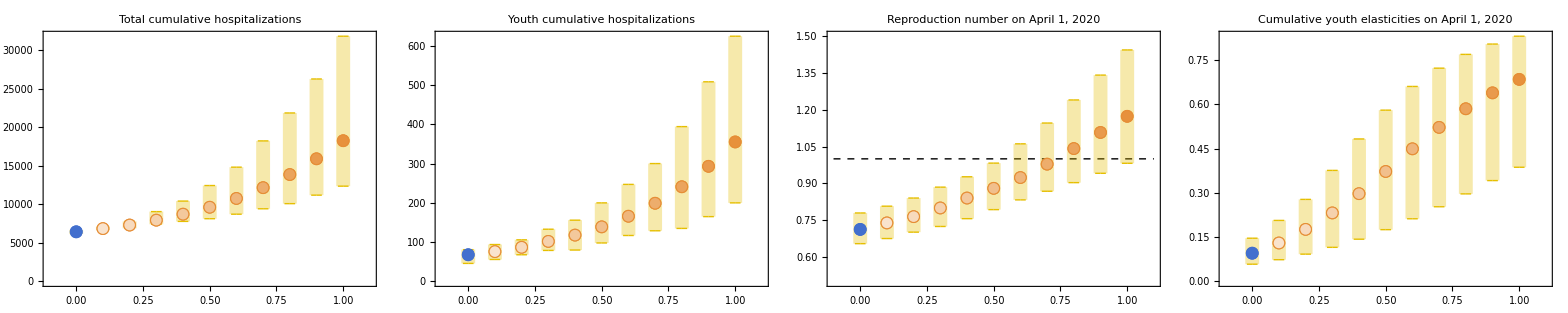
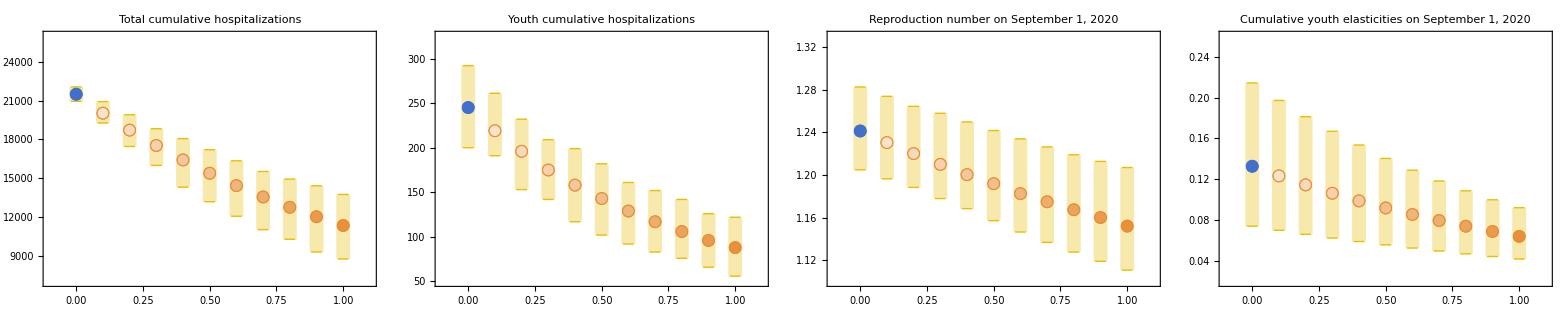
Scenario 1
Schools remained open | -Graphics-
Scenario 2
Schools remained closed | -Graphics-
 | School mitigation levels, 
 |

```mathematica
colorsToVary=Prepend[Table[Blend[{White,colorOrange},t],{t,Range[0.25,1,0.08]}], colorBlue];

plotScatterError[DATA2PLOT_,XVALS_,COLORS_,YLABEL_:"",TITLE_:"",ADDRTLINE_:False,YRANGE_:All]:=
ListPlot[{#}&/@Transpose[{XVALS,DATA2PLOT}],
PlotTheme->"Web",
PlotMarkers->Table[{Graphics[{EdgeForm[{If[i==1,colorBlue, colorOrange],Thick, Opacity[1]}],Disk[]}],12},{i,1,Length[COLORS]}],
PlotStyle->COLORS,
AspectRatio->0.5,
ImageSize->300,
IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->.02,"FenceStyle"->Directive[colorYellowBright,Thick],"WhiskerStyle"->Directive[CapForm["Butt"],AbsoluteThickness[10],Opacity[0.33],colorYellowBright]|>,
PlotRange->{{-0.1,1.1},YRANGE},
PlotLabel->Style[TITLE,FontSize->sizeFontBig,FontColor->Black,TextAlignment->Center],
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,sizeFontSmall],FrameLabel->If[YLABEL===None,{None,None},{None,Style[YLABEL,FontSize->sizeFontBig]}],
Prolog->If[ADDRTLINE==False,{},{Dashed,Black,Line[{{-0.1,1},{1.1,1}}]}]];

titlesScen1 = {"Total cumulative\nhospitalizations", "Youth cumulative\nhospitalizations", "Reproduction number\non April 1, 2020", "Cumulative youth elasticities\non April 1, 2020"};
titlesScen2 = {"Total cumulative\nhospitalizations", "Youth cumulative\nhospitalizations", "Reproduction number\non September 1, 2020", "Cumulative youth elasticities\non September 1, 2020"};
labelsScen1 = {"a","b","c","d"};
labelsScen2 = {"e","f","g","h"};

scen1Table = Table[plotWithLetter[plotScatterError[data2PlotScen1[[i]],Range[0,1,0.1],colorsToVary,None, titlesScen1[[i]],If[i==3,True,False],
If[i==3,{0.5,1.5},All]],labelsScen1[[i]],"lefter"], {i,1,4}];
scen2Table = Table[plotWithLetter[plotScatterError[data2PlotScen2[[i]],Range[0,1,0.1],colorsToVary,None, titlesScen2[[i]],False,
Which[i==1,{7000,26000},
i==2,{50,325},
i==3,{1.1,1.33},
i==4,{0.02,0.26},
True,All]],labelsScen2[[i]],"lefter"], {i,1,4}];

figVaryMultipliers = Grid[{{Style[Rotate["Scenario 1\nSchools remained open", Pi/2],colorOrange,sizeFontBig, FontFamily->"Helvetica",TextAlignment->Center],Grid[{scen1Table}]},
{Style[Rotate["Scenario 2\nSchools remained closed", Pi/2],colorOrange,sizeFontBig, FontFamily->"Helvetica",TextAlignment->Center],Grid[{scen2Table}]},
{"",Style["School mitigation levels, ",Black,sizeFontBig, FontFamily->"Helvetica"]},
{"",Row[{
PointLegend[{None},{Style["Baseline, median",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{EdgeForm[{colorBlue,Thick, Opacity[1]}],FaceForm[colorBlue],Disk[]}]}},LegendMarkerSize->12],
(*PointLegend[{None},{Style["Scenarios (1 & 2), median",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{EdgeForm[{colorOrange,Thick, Opacity[1]}],FaceForm[colorOrange],Disk[]}]}},LegendMarkerSize->12],*)
PointLegend[{None},{Style["Scenarios, median",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{EdgeForm[{colorOrange,Thick, Opacity[1]}],FaceForm[White],Disk[]}]}},LegendMarkerSize->12],
PointLegend[{Directive[colorYellowBright,Opacity[0.33],EdgeForm[{colorYellowBright, Thick, Opacity[1]}]]},{Style["95% CrI",FontSize->sizeFontSmall]},LegendMarkers->{Graphics[Rectangle[]]}]}]}}];

exportFigs[figVaryMultipliers, "Fig5"];
```

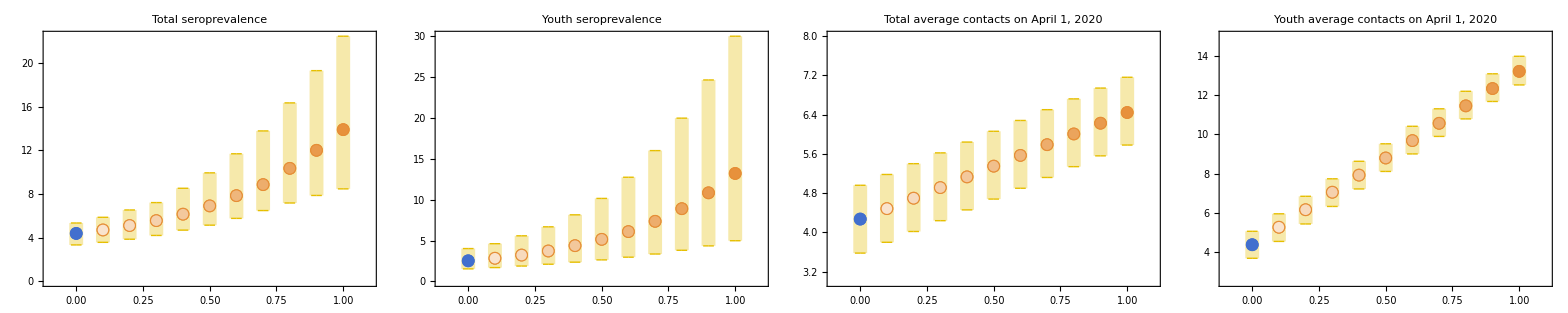
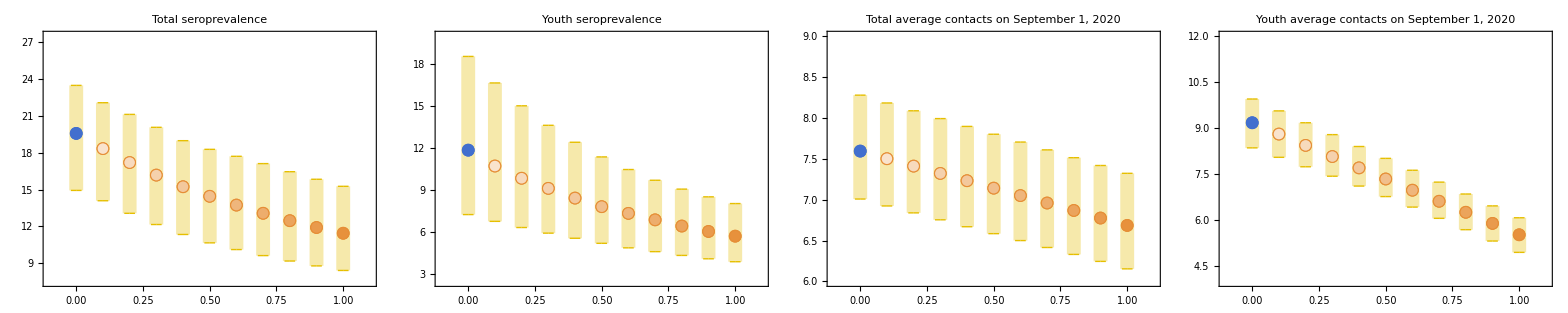
Scenario 1
Schools remained open | -Graphics-
Scenario 2
Schools remained closed | -Graphics-
 | School mitigation levels, 
 |

```mathematica
data2PlotScen1 = {seroScen1Total, seroScen1Youth, aveContsScen1Total, aveContsScen1Youth};
data2PlotScen2 = {seroScen2Total, seroScen2Youth, aveContsScen2Total, aveContsScen2Youth};

colorsToVary=Prepend[Table[Blend[{White,colorOrange},t],{t,Range[0.25,1,0.08]}], colorBlue];

titlesScen1 = {"Total\nseroprevalence", "Youth\nseroprevalence", "Total average contacts\non April 1, 2020", "Youth average contacts\non April 1, 2020"};
titlesScen2 = {"Total\nseroprevalence", "Youth\nseroprevalence", "Total average contacts\non September 1, 2020", "Youth average contacts\non September 1, 2020"};
labelsScen1 = {"a","b","c","d"};
labelsScen2 = {"e","f","g","h"};

scen1Table = Table[plotWithLetter[plotScatterError[data2PlotScen1[[i]],Range[0,1,0.1],colorsToVary,None, titlesScen1[[i]],False,
Which[i==3,{3,8},
i==4,{2.5,15},
True,All]],labelsScen1[[i]],"lefter"], {i,1,4}];
scen2Table = Table[plotWithLetter[plotScatterError[data2PlotScen2[[i]],Range[0,1,0.1],colorsToVary,None, titlesScen2[[i]],False,
Which[i==1,{7.5,27.5},
i==2,{2.5,20},
i==3,{6,9},
i==4,{4,12},
True,All]],labelsScen2[[i]],"lefter"], {i,1,4}];

figVaryMultipliers2 = Grid[{{Style[Rotate["Scenario 1\nSchools remained open", Pi/2],colorOrange,sizeFontBig, FontFamily->"Helvetica",TextAlignment->Center],Grid[{scen1Table}]},
{Style[Rotate["Scenario 2\nSchools remained closed", Pi/2],colorOrange,sizeFontBig, FontFamily->"Helvetica",TextAlignment->Center],Grid[{scen2Table}]},
{"",Style["School mitigation levels, ",Black,sizeFontBig, FontFamily->"Helvetica"]},
{"",Row[{
PointLegend[{None},{Style["Baseline, median",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{EdgeForm[{colorBlue,Thick, Opacity[1]}],FaceForm[colorBlue],Disk[]}]}},LegendMarkerSize->12],
(*PointLegend[{None},{Style["Scenarios (1 & 2), median",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{EdgeForm[{colorOrange,Thick, Opacity[1]}],FaceForm[colorOrange],Disk[]}]}},LegendMarkerSize->12],*)
PointLegend[{None},{Style["Scenarios, median",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{EdgeForm[{colorOrange,Thick, Opacity[1]}],FaceForm[White],Disk[]}]}},LegendMarkerSize->12],
PointLegend[{Directive[colorYellowBright,Opacity[0.33],EdgeForm[{colorYellowBright, Thick, Opacity[1]}]]},{Style["95% CrI",FontSize->sizeFontSmall]},LegendMarkers->{Graphics[Rectangle[]]}]}]}}];

exportFigs[figVaryMultipliers2, "SFig20"];
```

```mathematica
alphabet = {"=0.10", "=0.20","=0.30","=0.40","=0.50","=0.60","=0.70","=0.80","=0.90"};

figuresScen1Total = Table[plotWithLetter[{
plotLineWithCrI[hospitalizationSimulatedScenariosTotal[[scen1Idx[[1]],1, All, All]],colorBlue,"","","",1,If[i<7,ticksInvisible,ticksVisible],{0, 500},0.33,400,Solid,hospitalizationScenariosTotal[[scen1Idx[[1]],1, All, All]]],
plotLineWithCrI[hospitalizationSimulatedScenariosTotal[[scen1Idx[[i+1]],1, All, All]],colorOrange,"","","",1,ticksVisible,{0, 500},0.33,400,Solid,hospitalizationScenariosTotal[[scen1Idx[[i+1]],1, All, All]]]},alphabet[[i]],Scaled[{0.8,0.9}]], {i, 1, 9}];
figuresScen1Youth= Table[plotWithLetter[{
plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[scen1Idx[[1]],1, All, All]],colorBlue,"","","",1,If[i<7,ticksInvisible,ticksVisible],{0, 18},0.33,400,Solid,hospitalizationScenariosGrouped[[scen1Idx[[1]],1, All, All]]],
plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[scen1Idx[[i+1]],1, All, All]],colorOrange,"","","",1,ticksVisible,{0, 18},0.33,400,Solid,hospitalizationScenariosGrouped[[scen1Idx[[i+1]],1, All, All]]]},alphabet[[i]],Scaled[{0.8,0.9}]], {i, 1, 9}];
```

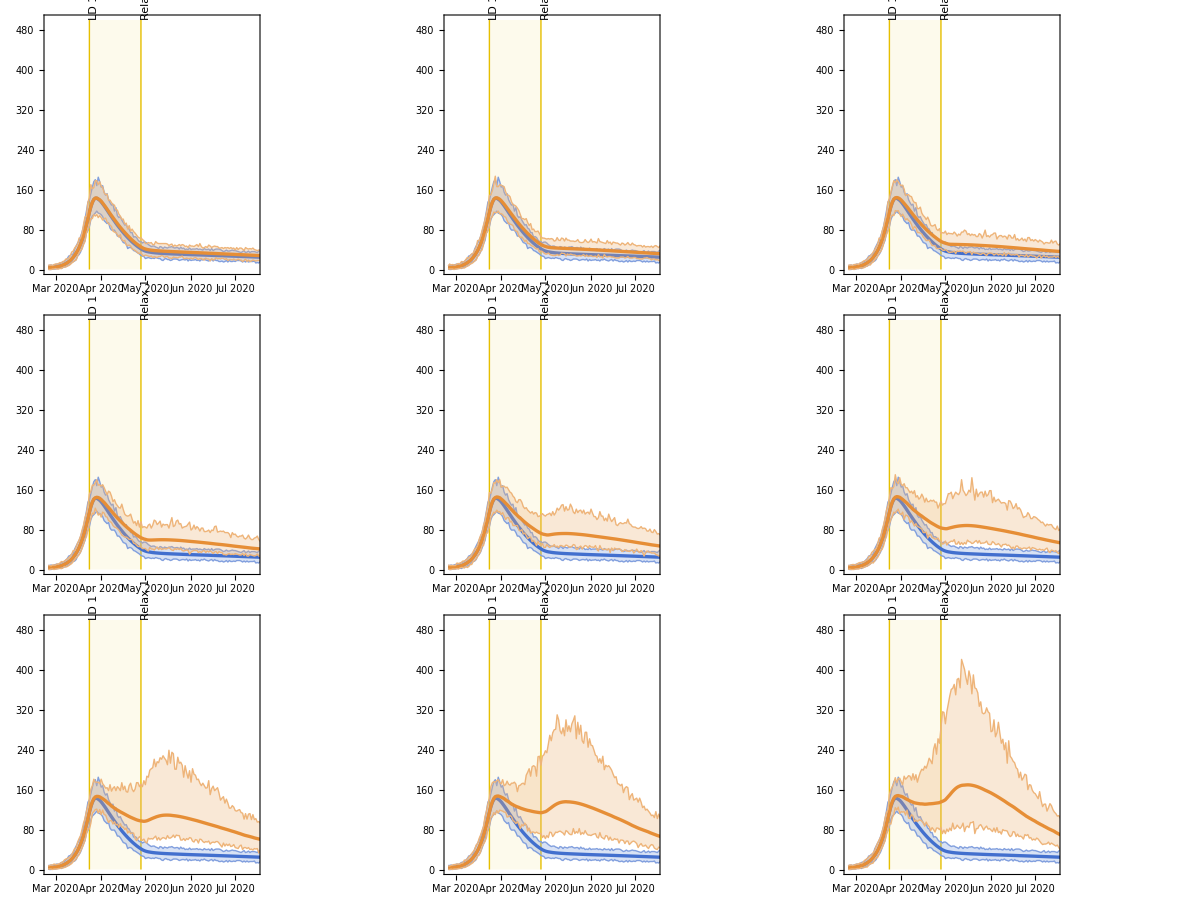
| Scenario 1
Schools remained open
Total hospitalizations (1/day) | -Graphics-
 |

```mathematica
figS1Total=Grid[{{"", Style["Scenario 1\nSchools remained open",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Total hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figuresScen1Total,{3,3}]]},
{"", legendRawScen1ElasFlat}}];
exportFigs[figS1Total, "SFig21"];
```

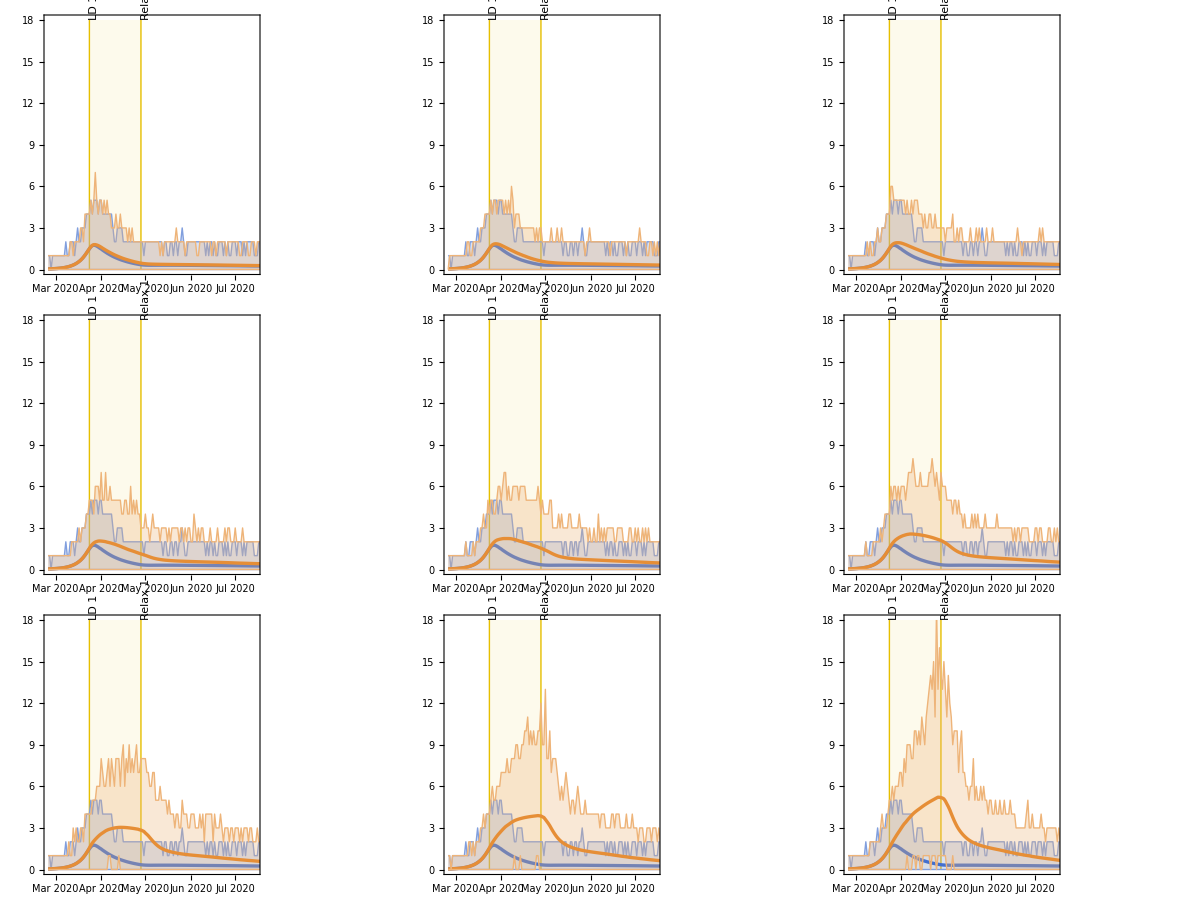
| Scenario 1
Schools remained open
Youth hospitalizations (1/day) | -Graphics-
 |

```mathematica
figS1Youth=Grid[{{"", Style["Scenario 1\nSchools remained open",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Youth hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figuresScen1Youth,{3,3}]]},
{"", legendRawScen1ElasFlat}}];
exportFigs[figS1Youth, "SFig22"];
```

```mathematica
alphabet = {"=0.10", "=0.20","=0.30","=0.40","=0.50","=0.60","=0.70","=0.80","=0.90"};

figuresScen2Total = Table[plotWithLetter[{
plotLineWithCrI[hospitalizationSimulatedScenariosTotal[[scen2Idx[[1]],1, All, All]],colorBlue,"","","",2,If[i<7,ticksInvisible,ticksVisible],{0, 350},0.33,400,Solid,hospitalizationScenariosTotal[[scen2Idx[[1]],1, All, All]]],
plotLineWithCrI[hospitalizationSimulatedScenariosTotal[[scen2Idx[[i+1]],1, All, All]],colorOrange,"","","",2,ticksVisible,{0, 350},0.33,400,Solid,hospitalizationScenariosTotal[[scen2Idx[[i+1]],1, All, All]]]},alphabet[[i]],Scaled[{0.1,0.9}]], {i, 1, 9}];
figuresScen2Youth= Table[plotWithLetter[{
plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[scen2Idx[[1]],1, All, All]],colorBlue,"","","",2,If[i<7,ticksInvisible,ticksVisible],{0, 10},0.33,400,Solid,hospitalizationScenariosGrouped[[scen2Idx[[1]],1, All, All]]],
plotLineWithCrI[hospitalizationSimulatedScenariosGrouped[[scen2Idx[[i+1]],1, All, All]],colorOrange,"","","",2,ticksVisible,{0, 10},0.33,400,Solid,hospitalizationScenariosGrouped[[scen2Idx[[i+1]],1, All, All]]]},alphabet[[i]],Scaled[{0.1,0.9}]], {i, 1, 9}];
```

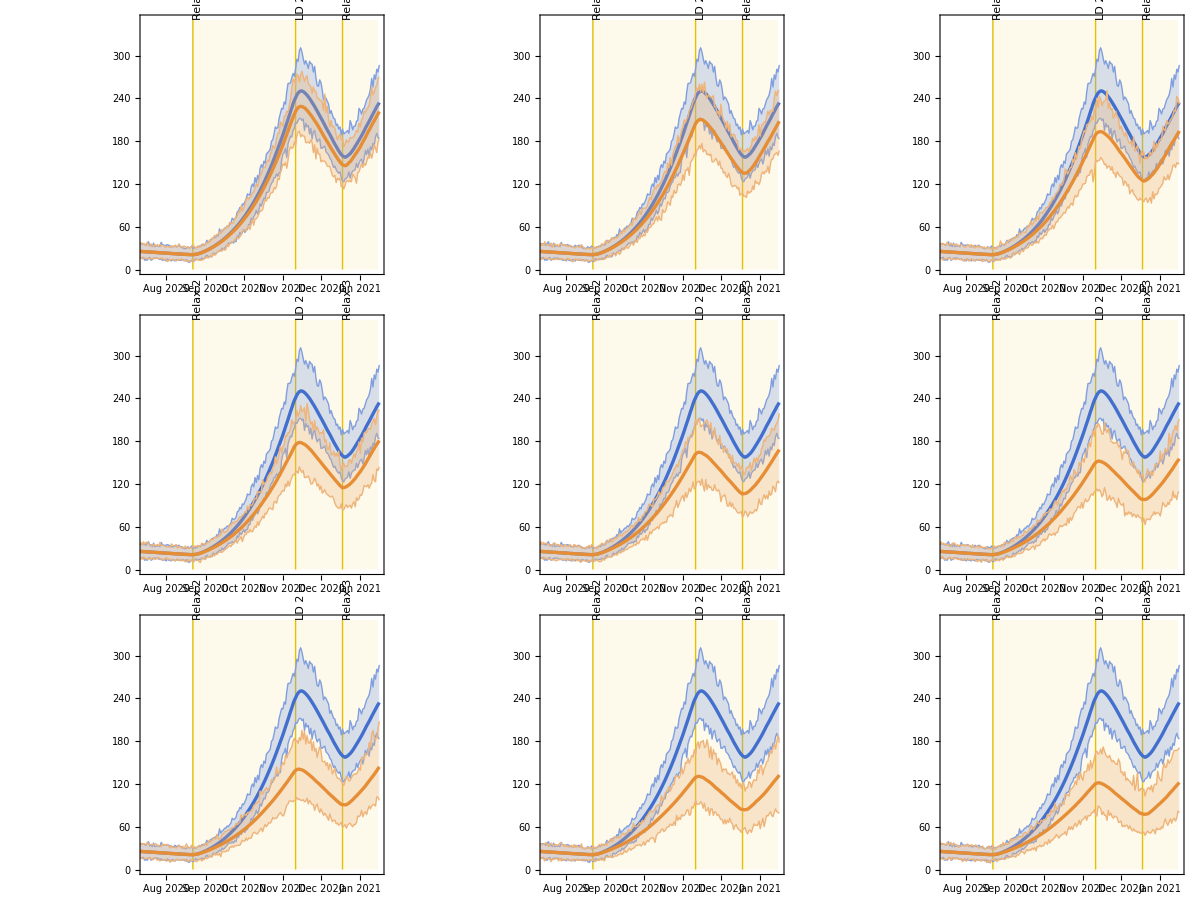
| Scenario 2
Schools remained closed
Total hospitalizations (1/day) | -Graphics-
 |

```mathematica
figS2Total=Grid[{{"", Style["Scenario 2\nSchools remained closed",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Total hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figuresScen2Total,{3,3}]]},
{"", legendRawScen2ElasFlat}}];
exportFigs[figS2Total, "SFig23"];
```

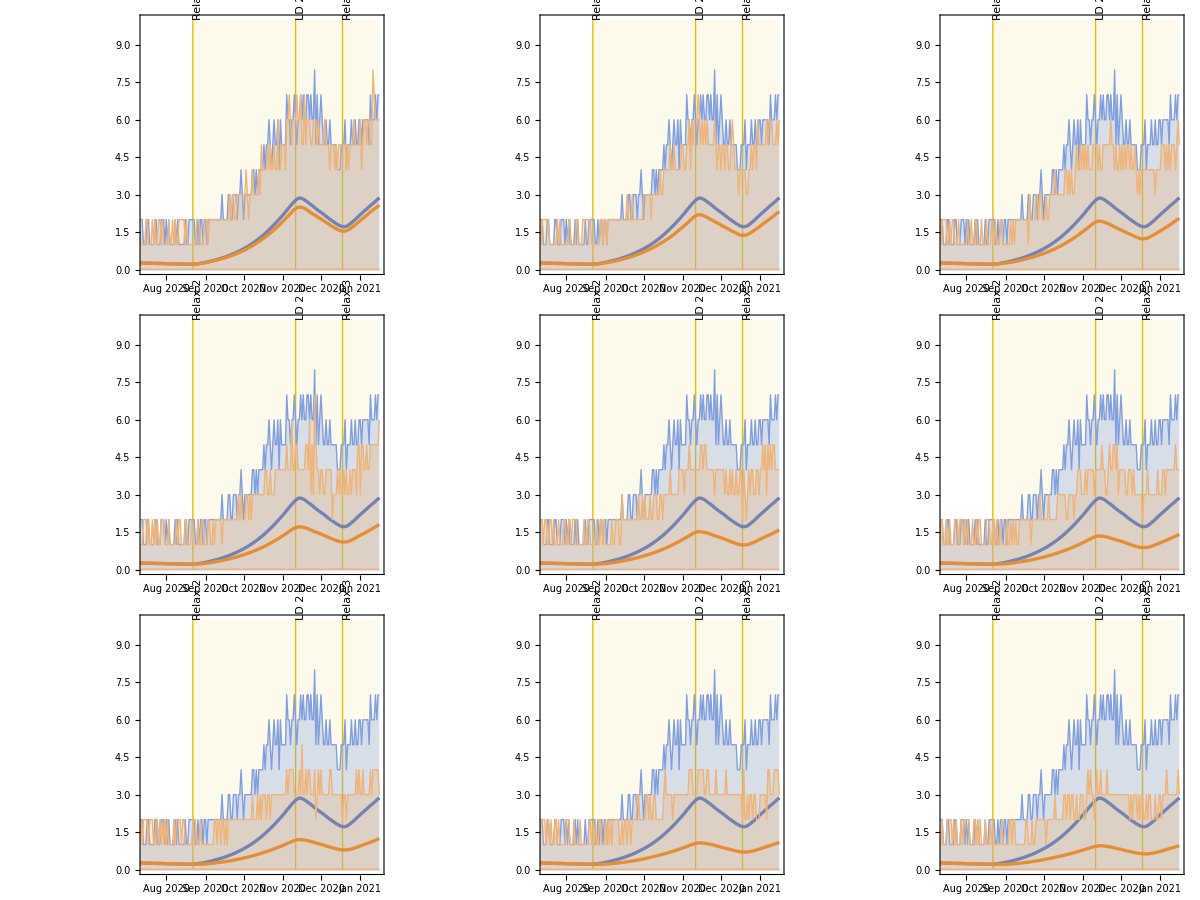
| Scenario 2
Schools remained closed
Youth hospitalizations (1/day) | -Graphics-
 |

```mathematica
figS2Youth=Grid[{{"", Style["Scenario 2\nSchools remained closed",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Youth hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figuresScen2Youth,{3,3}]]},
{"", legendRawScen2ElasFlat}}];
exportFigs[figS2Youth, "SFig24"];
```

## Tables

```mathematica
timeIndex1 = 36; (*Apr 1 2020*)
timeIndex2 = 189;(*Sep 1 2020*)
timeEnd1= 141;
timeEnd2 = 325;
timeEnd2Adjusted = timeEnd2-30;
```

```mathematica
getAroundMedian[data_,data2_:Automatic]:=Module[{actualData2,numData1,numData2},
actualData2=If[data2===Automatic,data,data2];
numData1=If[MatchQ[data[[1]],_DateObject],AbsoluteTime/@data,data];
numData2=If[MatchQ[actualData2[[1]],_DateObject],AbsoluteTime/@actualData2,actualData2];
Around[Median[numData1],{Median[numData2]-Quantile[numData2,0.025],Quantile[numData2,0.975]-Median[numData2]}]];
```

```mathematica
hospMatrices = {hospitalizationScenariosGrouped,hospitalizationScenariosTotal, hospitalizationSimulatedScenariosGrouped, hospitalizationSimulatedScenariosTotal};
startDate=DateObject[{2020,2,25}];

getPeaks[singleDataMatrix_,scenarioLabel_String]:=
Module[{startDay,endDay,allPeakValues,allPeakIndices,allPeakDates},
Switch[scenarioLabel,
"Scenario 1",startDay=1;endDay=timeEnd1;,
"Scenario 2",startDay=timeEnd1+1;endDay=timeEnd2Adjusted;,
_,startDay=1;endDay=timeEnd2Adjusted;];

allPeakValues=Map[Max[#[[startDay;;endDay]]]&,singleDataMatrix,{-2}];
allPeakIndices=Map[Ordering[#[[startDay;;endDay]],-1][[1]]+startDay-1&,singleDataMatrix,{-2}];
allPeakDates=Map[DatePlus[startDate,#-1]&,allPeakIndices,{-1}];

{allPeakValues,allPeakDates}];

hospPeakResults1=getPeaks[#,"Scenario 1"]&/@hospMatrices;
hospPeakResults2=getPeaks[#,"Scenario 2"]&/@hospMatrices;
```

```mathematica
hospScen1PeakValTotal = Table[getAroundMedian[hospPeakResults1[[2]][[1,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[4]][[1,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen1PeakDateTotal = Table[getAroundMedian[hospPeakResults1[[2]][[2,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[4]][[2,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen1PeakValYouth =Table[getAroundMedian[hospPeakResults1[[1]][[1,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[3]][[1,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen1PeakDateYouth = Table[getAroundMedian[hospPeakResults1[[1]][[2,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[3]][[2,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen2PeakValTotal = Table[getAroundMedian[hospPeakResults2[[2]][[1,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[4]][[1,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];
hospScen2PeakDateTotal = Table[getAroundMedian[hospPeakResults2[[2]][[2,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[4]][[2,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];
hospScen2PeakValYouth = Table[getAroundMedian[hospPeakResults2[[1]][[1,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[3]][[1,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];
hospScen2PeakDateYouth = Table[getAroundMedian[hospPeakResults2[[1]][[2,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[3]][[2,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];

scenario1Summary = {cumuHospScen1Total,hospScen1PeakValTotal,hospScen1PeakDateTotal, cumuHospScen1Youth,hospScen1PeakValYouth,hospScen1PeakDateYouth,seroScen1Total,seroScen1Youth, aveContsScen1Total, aveContsScen1Youth, RtScen1, cumuElasScen1Youth};
scenario2Summary = {cumuHospScen2Total, hospScen2PeakValTotal,hospScen2PeakDateTotal, cumuHospScen2Youth,hospScen2PeakValYouth,hospScen2PeakDateYouth,seroScen2Total,seroScen2Youth, aveContsScen2Total, aveContsScen2Youth, RtScen2, cumuElasScen2Youth};
```

```mathematica
dataTableLabels1={"Total, hosp cumu","Total, hosp peak val. (<2021)","Total, hosp peak date (<2021)", "Youth, hosp cumu","Youth, hosp peak val. (<2021)","Youth, hosp peak date (<2021)", "Total, sero end", "Youth, sero end", "Total, conts Apr 1", "Youth, conts Apr 1", "Rep no, Apr 1", "Youth elas, Apr 1"};
dataTableLabels2={"Total, hosp cumu","Total, hosp peak val. (<2021)","Total, hosp peak date (<2021)", "Youth, hosp cumu","Youth, hosp peak val. (<2021)","Youth, hosp peak date (<2021)", "Total, sero end", "Youth, sero end", "Total, conts Sep 1", "Youth, conts Sep 1", "Rep no, Sep 1", "Youth elas, Sep 1"};

formatItem[a_,rowIndex_]:=Module[{val,minInt,maxInt,isHospRow,formatNum},If[a["Value"]>1000000,(*Date formatting remains untouched*)DateString[a["Value"],{"MonthNameShort"," ","Day"}]<>" ("<>DateString[Min[a["Interval"]],{"MonthNameShort"," ","Day"}]<>" - "<>DateString[Max[a["Interval"]],{"MonthNameShort"," ","Day"}]<>")",(*Floor values to zero (prevent negatives)*)val=Max[0,a["Value"]];
minInt=Max[0,Min[a["Interval"]]];
maxInt=Max[0,Max[a["Interval"]]];
(*Identify if the current item is a hospitalization metric (whole numbers)*)isHospRow=MemberQ[{1,2,4,5},rowIndex];
(*Helper function to format the number strings accordingly*)formatNum[x_]:=If[isHospRow,ToString[Round[x]],ToString[NumberForm[x,{Infinity,2}]]];
(*Apply the formatting and concatenate*)formatNum[val]<>" ("<>formatNum[minInt]<>" - "<>formatNum[maxInt]<>")"]];
```

```mathematica
dataTableFormatted1=MapIndexed[formatItem[#1,#2[[1]]]&,scenario1Summary,{2}];
dataTableFinal1=MapThread[Prepend,{dataTableFormatted1,dataTableLabels1}];

dataTableFormatted2=MapIndexed[formatItem[#1,#2[[1]]]&,scenario2Summary,{2}];
dataTableFinal2=MapThread[Prepend,{dataTableFormatted2,dataTableLabels2}];

columnHeadings=Join[{"Model outcome", "Baseline"}, alphabet, {"Scenario 1"}];
TableForm[MapThread[Join,{dataTableFinal1}],TableHeadings->{None,columnHeadings}]
```

Model outcome | Baseline | =0.10 | =0.20 | =0.30 | =0.40 | =0.50 | =0.60 | =0.70 | =0.80 | =0.90 | Scenario 1
Total, hosp cumu | 6452 (6161 - 6706) | 6868 (6629 - 7179) | 7329 (6895 - 7810) | 7965 (7432 - 9075) | 8741 (7805 - 10443) | 9643 (8153 - 12461) | 10783 (8740 - 14847) | 12184 (9442 - 18258) | 13888 (10109 - 21886) | 15935 (11212 - 26299) | 18283 (12379 - 31854)
Total, hosp peak val. (<2021) | 143 (126 - 169) | 144 (127 - 170) | 144 (129 - 171) | 145 (123 - 173) | 145 (129 - 170) | 146 (129 - 173) | 147 (128 - 180) | 149 (132 - 221) | 153 (125 - 290) | 170 (124 - 409) | 213 (120 - 563)
Total, hosp peak date (<2021) | Mar 29 (Mar 25 - Apr 02) | Mar 29 (Mar 24 - Apr 03) | Mar 29 (Mar 25 - Apr 04) | Mar 29 (Mar 24 - Apr 02) | Mar 29 (Mar 24 - Apr 06) | Mar 29 (Mar 24 - Apr 05) | Mar 29 (Mar 23 - May 17) | Mar 30 (Mar 24 - May 28) | Mar 30 (Mar 03 - May 05) | May 14 (Mar 26 - May 30) | May 14 (Mar 27 - May 26)
Youth, hosp cumu | 68 (46 - 81) | 76 (56 - 94) | 87 (68 - 106) | 102 (79 - 133) | 118 (80 - 156) | 139 (98 - 200) | 166 (117 - 247) | 199 (129 - 300) | 241 (135 - 394) | 293 (165 - 508) | 355 (200 - 624)
Youth, hosp peak val. (<2021) | 2 (1 - 4) | 2 (1 - 5) | 2 (1 - 5) | 2 (0 - 4) | 2 (1 - 5) | 2 (0 - 5) | 3 (1 - 7) | 3 (1 - 8) | 4 (0 - 12) | 5 (1 - 14) | 7 (2 - 19)
Youth, hosp peak date (<2021) | Mar 27 (Mar 16 - May 08) | Mar 28 (Mar 15 - Jun 13) | Mar 28 (Mar 17 - Jun 02) | Mar 29 (Mar 15 - Jun 22) | Mar 31 (Mar 15 - May 08) | Apr 03 (Mar 18 - Jun 03) | Apr 08 (Mar 17 - Apr 25) | Apr 15 (Mar 20 - May 03) | Apr 26 (Apr 04 - May 12) | Apr 28 (Apr 06 - May 08) | Apr 28 (Apr 07 - May 09)
Total, sero end | 4.40 (3.35 - 5.35) | 4.71 (3.58 - 5.87) | 5.12 (3.87 - 6.54) | 5.57 (4.21 - 7.22) | 6.16 (4.70 - 8.53) | 6.92 (5.15 - 9.94) | 7.85 (5.77 - 11.68) | 8.86 (6.49 - 13.78) | 10.35 (7.18 - 16.34) | 12.00 (7.87 - 19.29) | 13.89 (8.47 - 22.44)
Youth, sero end | 2.52 (1.54 - 4.02) | 2.84 (1.70 - 4.61) | 3.23 (1.88 - 5.58) | 3.72 (2.11 - 6.68) | 4.37 (2.36 - 8.14) | 5.15 (2.64 - 10.14) | 6.09 (2.97 - 12.73) | 7.35 (3.35 - 15.98) | 8.89 (3.81 - 19.94) | 10.83 (4.35 - 24.61) | 13.19 (4.98 - 29.95)
Total, conts Apr 1 | 4.27 (3.58 - 4.96) | 4.49 (3.80 - 5.18) | 4.70 (4.02 - 5.40) | 4.91 (4.24 - 5.62) | 5.13 (4.46 - 5.84) | 5.35 (4.68 - 6.06) | 5.57 (4.90 - 6.28) | 5.79 (5.12 - 6.50) | 6.01 (5.34 - 6.72) | 6.23 (5.56 - 6.94) | 6.44 (5.78 - 7.16)
Youth, conts Apr 1 | 4.37 (3.68 - 5.06) | 5.26 (4.54 - 5.95) | 6.16 (5.43 - 6.84) | 7.05 (6.32 - 7.73) | 7.92 (7.22 - 8.63) | 8.79 (8.11 - 9.52) | 9.68 (9.00 - 10.41) | 10.56 (9.89 - 11.30) | 11.45 (10.79 - 12.19) | 12.33 (11.67 - 13.08) | 13.21 (12.52 - 13.98)
Rep no, Apr 1 | 0.71 (0.65 - 0.78) | 0.74 (0.68 - 0.81) | 0.76 (0.70 - 0.84) | 0.80 (0.72 - 0.88) | 0.84 (0.76 - 0.93) | 0.88 (0.79 - 0.98) | 0.92 (0.83 - 1.06) | 0.98 (0.87 - 1.15) | 1.04 (0.90 - 1.24) | 1.11 (0.94 - 1.34) | 1.17 (0.98 - 1.44)
Youth elas, Apr 1 | 0.10 (0.06 - 0.15) | 0.13 (0.07 - 0.21) | 0.18 (0.09 - 0.28) | 0.23 (0.12 - 0.38) | 0.30 (0.14 - 0.48) | 0.37 (0.18 - 0.58) | 0.45 (0.21 - 0.66) | 0.52 (0.25 - 0.72) | 0.58 (0.30 - 0.77) | 0.64 (0.34 - 0.80) | 0.68 (0.39 - 0.83)

```mathematica
columnHeadings=Join[{"Model outcome", "Baseline"}, alphabet, {"Scenario 2"}];
TableForm[MapThread[Join,{dataTableFinal2}],TableHeadings->{None,columnHeadings}]
```

Model outcome | Baseline | =0.10 | =0.20 | =0.30 | =0.40 | =0.50 | =0.60 | =0.70 | =0.80 | =0.90 | Scenario 2
Total, hosp cumu | 21507 (20955 - 22075) | 20036 (19275 - 20935) | 18725 (17457 - 19920) | 17531 (15991 - 18836) | 16417 (14307 - 18067) | 15385 (13180 - 17210) | 14425 (12054 - 16347) | 13546 (11014 - 15523) | 12749 (10271 - 14934) | 12017 (9286 - 14414) | 11336 (8742 - 13742)
Total, hosp peak val. (<2021) | 251 (227 - 286) | 229 (212 - 270) | 211 (185 - 257) | 194 (162 - 240) | 178 (146 - 210) | 165 (133 - 203) | 152 (113 - 193) | 141 (103 - 185) | 131 (97 - 182) | 122 (88 - 154) | 114 (74 - 145)
Total, hosp peak date (<2021) | Nov 15 (Nov 08 - Nov 24) | Nov 15 (Nov 07 - Nov 26) | Nov 15 (Nov 07 - Nov 26) | Nov 15 (Nov 06 - Nov 26) | Nov 15 (Nov 07 - Nov 24) | Nov 15 (Nov 04 - Nov 22) | Nov 14 (Nov 06 - Nov 23) | Nov 14 (Nov 04 - Nov 23) | Nov 14 (Nov 04 - Nov 27) | Nov 14 (Nov 02 - Nov 27) | Nov 14 (Nov 03 - Nov 27)
Youth, hosp cumu | 245 (200 - 292) | 219 (191 - 261) | 196 (153 - 232) | 175 (142 - 209) | 158 (117 - 199) | 143 (102 - 182) | 129 (92 - 161) | 117 (83 - 152) | 106 (76 - 142) | 96 (66 - 126) | 88 (56 - 122)
Youth, hosp peak val. (<2021) | 3 (2 - 6) | 3 (2 - 5) | 2 (1 - 5) | 2 (1 - 4) | 2 (0 - 4) | 2 (1 - 4) | 1 (0 - 3) | 1 (0 - 2) | 1 (0 - 3) | 1 (0 - 3) | 1 (0 - 3)
Youth, hosp peak date (<2021) | Nov 14 (Oct 12 - Dec 07) | Nov 14 (Oct 22 - Dec 07) | Nov 14 (Oct 20 - Dec 08) | Nov 14 (Oct 17 - Dec 04) | Nov 14 (Oct 14 - Dec 06) | Nov 14 (Oct 08 - Dec 08) | Nov 15 (Oct 01 - Dec 03) | Nov 15 (Sep 29 - Dec 04) | Nov 15 (Sep 29 - Dec 08) | Nov 15 (Aug 02 - Dec 06) | Nov 15 (Sep 18 - Dec 06)
Total, sero end | 19.57 (14.93 - 23.49) | 18.33 (14.08 - 22.08) | 17.20 (13.06 - 21.12) | 16.17 (12.15 - 20.07) | 15.23 (11.33 - 18.98) | 14.45 (10.65 - 18.27) | 13.73 (10.10 - 17.71) | 13.06 (9.61 - 17.11) | 12.46 (9.17 - 16.45) | 11.90 (8.77 - 15.84) | 11.43 (8.40 - 15.26)
Youth, sero end | 11.87 (7.27 - 18.56) | 10.74 (6.79 - 16.67) | 9.87 (6.35 - 15.03) | 9.14 (5.95 - 13.64) | 8.45 (5.58 - 12.43) | 7.84 (5.22 - 11.39) | 7.36 (4.90 - 10.49) | 6.90 (4.63 - 9.72) | 6.46 (4.36 - 9.09) | 6.07 (4.12 - 8.54) | 5.73 (3.91 - 8.06)
Total, conts Sep 1 | 7.59 (7.01 - 8.28) | 7.50 (6.92 - 8.18) | 7.41 (6.84 - 8.09) | 7.32 (6.75 - 7.99) | 7.23 (6.67 - 7.90) | 7.14 (6.59 - 7.80) | 7.05 (6.50 - 7.71) | 6.96 (6.42 - 7.61) | 6.87 (6.33 - 7.51) | 6.78 (6.25 - 7.42) | 6.69 (6.15 - 7.32)
Youth, conts Sep 1 | 9.18 (8.36 - 9.95) | 8.81 (8.05 - 9.56) | 8.44 (7.74 - 9.18) | 8.08 (7.43 - 8.79) | 7.71 (7.11 - 8.40) | 7.34 (6.77 - 8.02) | 6.98 (6.43 - 7.63) | 6.62 (6.06 - 7.24) | 6.26 (5.69 - 6.85) | 5.89 (5.32 - 6.47) | 5.52 (4.95 - 6.08)
Rep no, Sep 1 | 1.24 (1.20 - 1.28) | 1.23 (1.20 - 1.27) | 1.22 (1.19 - 1.26) | 1.21 (1.18 - 1.26) | 1.20 (1.17 - 1.25) | 1.19 (1.16 - 1.24) | 1.18 (1.15 - 1.23) | 1.17 (1.14 - 1.23) | 1.17 (1.13 - 1.22) | 1.16 (1.12 - 1.21) | 1.15 (1.11 - 1.21)
Youth elas, Sep 1 | 0.13 (0.07 - 0.21) | 0.12 (0.07 - 0.20) | 0.11 (0.07 - 0.18) | 0.11 (0.06 - 0.17) | 0.10 (0.06 - 0.15) | 0.09 (0.06 - 0.14) | 0.09 (0.05 - 0.13) | 0.08 (0.05 - 0.12) | 0.07 (0.05 - 0.11) | 0.07 (0.04 - 0.10) | 0.06 (0.04 - 0.09)